```mathematica
k:=1;g:=-1;h:=1/n;ρ:=1;n:=14
s[x_]=0.96-0.25(x-0.5)^2
```

0.96-0.25 (-0.5+x)^2

```mathematica
yvec:=Table[Subscript[y, i],{i,1,n-1}];
λvec:=Table[λi,{i,1,n-1}];
xs:=Table[(1/n)i,{i,1,n-1}]
```

```mathematica
eq1:={Piecewise[{{(-1+2*yvec[[1]]-yvec[[2]])/h^2+1+λvec[[1]]+ρ*(yvec[[1]]-s[xs[[1]]])==0,λvec[[1]]+ρ*(yvec[[1]]-s[xs[[1]]])≤0},{(-1+2*yvec[[1]]-yvec[[2]])/h^2+1==0,λvec[[1]]+ρ*(yvec[[1]]-s[xs[[1]]])>0}}]};
eqn:={Piecewise[{{(-1+2*yvec[[n-1]]-yvec[[n-2]])/h^2+1+λvec[[n-1]]+ρ*(yvec[[n-1]]-s[xs[[n-1]]])==0,λvec[[n-1]]+ρ*(yvec[[n-1]]-s[xs[[n-1]]])≤0},{(-1+2*yvec[[n-1]]-yvec[[n-1]])/h^2+1==0,λvec[[n-1]]+ρ*(yvec[[n-1]]-s[xs[[n-1]]])>0}}]};
eqs1:=Table[Piecewise[{{(-yvec[[i-1]]+2*yvec[[i]]-yvec[[i+1]])/h^2+1+λvec[[i]]+ρ*(yvec[[i]]-s[xs[[i]]])==0,λvec[[i]]+ρ*(yvec[[i]]-s[xs[[i]]])≤0},{(-yvec[[i-1]]+2*yvec[[i]]-yvec[[i+1]])/h^2+1==0,λvec[[i]]+ρ*(yvec[[i]]-s[xs[[i]]])>0}}],{i,2,n-2}];
eqs2:=Table[Piecewise[{{yvec[[i]]-s[xs[[i]]]==0, λvec[[i]]+ρ*(yvec[[i]]-s[xs[[i]]])≤0},{-λvec[[i]]/ρ==0,λvec[[i]]+ρ*(yvec[[i]]-s[xs[[i]]])>0}}],{i,1,n-1}]
```

```mathematica
res=Solve[Join[eq1,eqn,eqs1,eqs2],Join[yvec,λvec]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{y_1→0.980776,y_2→0.966653,y_3→0.957633,y_4→0.953714,y_5→0.954898,y_6→0.958724,y_7→0.96,y_8→0.958724,y_9→0.955755,y_10→0.957888,y_11→0.965122,y_12→0.977459,y_13→0.994898,λ1→0,λ2→0,λ3→0,λ4→0,λ5→-0.482,λ6→-1.5,λ7→-1.5,λ8→-1.332,λ9→0,λ10→0,λ11→0,λ12→0,λ13→0}}

```mathematica
ys:=Table[res[[1,i,2]],{i,1,n-1}]
```

```mathematica
xplot:=Join[{0},xs,{1}];yplot:=Join[{1},ys,{1}]
```

```mathematica
str:=ListLinePlot[Transpose[{xplot,yplot}],Frame->True,PlotStyle->{Orange,Dashed}]
```

```mathematica
st:=RegionPlot[{y<s[x]&&y≥0},{x,0,1},{y,0,1},ColorFunction->Function[{x,y},ColorData["PigeonTones"][Sin[x]Sin[y]]],BoundaryStyle->None]
```

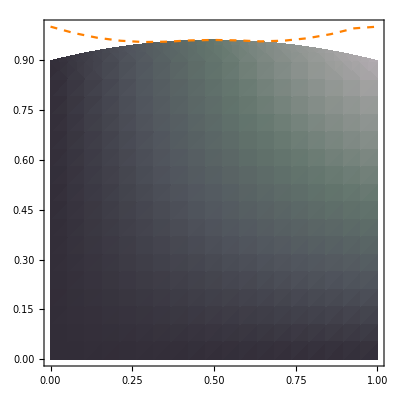

```mathematica
Show[st,str,AspectRatio->1,PlotRange->All]
```